```mathematica
PathPoly[n_]:=PathPoly[n]=ChromaticPolynomial[PathGraph[Range[n]],x]
```

```mathematica
PathBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = PathPoly[pos];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
PathBaseCoeff[Chromial[10]]
```

{0,0,32,-112,160,-120,50,-11,1}

```mathematica
CycleBaseCoeff[Chromial[10]]
```

{0,0,-80,48,40,-70,39,-10,1}

```mathematica
PathGraph[10]
```

PathGraph[10]

```mathematica
Clear[PathPoly]
```

```mathematica
CachePathProblem[n_]:=CachePathProblem[n]=With[
{P=Chromial[n]},
Problem[CoefficientList[P,x],PathBaseCoeff[P]]
]
```

```mathematica
DeleteDuplicates[
Monitor[
Table[
CacheProblem[k],{k,1000,1010}]
,k]
]
```

{{326 x1m10-27 x1m11+x1m12+13122 x1m2-54675 x1m3+99873 x1m4-105948 x1m5+72576 x1m6-33642 x1m7+10710 x1m8-2316 x1m9,326 x2m10-27 x2m11+x2m12+13122 x2m2-54675 x2m3+99873 x2m4-105948 x2m5+72576 x2m6-33642 x2m7+10710 x2m8-2316 x2m9,326 x3m10-27 x3m11+x3m12+13122 x3m2-54675 x3m3+99873 x3m4-105948 x3m5+72576 x3m6-33642 x3m7+10710 x3m8-2316 x3m9,326 x4m10-27 x4m11+x4m12+13122 x4m2-54675 x4m3+99873 x4m4-105948 x4m5+72576 x4m6-33642 x4m7+10710 x4m8-2316 x4m9,326 x5m10-27 x5m11+x5m12+13122 x5m2-54675 x5m3+99873 x5m4-105948 x5m5+72576 x5m6-33642 x5m7+10710 x5m8-2316 x5m9,326 x6m10-27 x6m11+x6m12+13122 x6m2-54675 x6m3+99873 x6m4-105948 x6m5+72576 x6m6-33642 x6m7+10710 x6m8-2316 x6m9,326 x7m10-27 x7m11+x7m12+13122 x7m2-54675 x7m3+99873 x7m4-105948 x7m5+72576 x7m6-33642 x7m7+10710 x7m8-2316 x7m9,326 x8m10-27 x8m11+x8m12+13122 x8m2-54675 x8m3+99873 x8m4-105948 x8m5+72576 x8m6-33642 x8m7+10710 x8m8-2316 x8m9,326 x9m10-27 x9m11+x9m12+13122 x9m2-54675 x9m3+99873 x9m4-105948 x9m5+72576 x9m6-33642 x9m7+10710 x9m8-2316 x9m9,326 x10m10-27 x10m11+x10m12+13122 x10m2-54675 x10m3+99873 x10m4-105948 x10m5+72576 x10m6-33642 x10m7+10710 x10m8-2316 x10m9,326 x11m10-27 x11m11+x11m12+13122 x11m2-54675 x11m3+99873 x11m4-105948 x11m5+72576 x11m6-33642 x11m7+10710 x11m8-2316 x11m9,326 x12m10-27 x12m11+x12m12+13122 x12m2-54675 x12m3+99873 x12m4-105948 x12m5+72576 x12m6-33642 x12m7+10710 x12m8-2316 x12m9}=={0,0,-256,1280,-2816,3584,-2912,1568,-560,128,-17,1},{328 x1m10-27 x1m11+x1m12+15552 x1m2-63342 x1m3+112941 x1m4-116919 x1m5+78216 x1m6-35467 x1m7+11074 x1m8-2357 x1m9,328 x2m10-27 x2m11+x2m12+15552 x2m2-63342 x2m3+112941 x2m4-116919 x2m5+78216 x2m6-35467 x2m7+11074 x2m8-2357 x2m9,328 x3m10-27 x3m11+x3m12+15552 x3m2-63342 x3m3+112941 x3m4-116919 x3m5+78216 x3m6-35467 x3m7+11074 x3m8-2357 x3m9,328 x4m10-27 x4m11+x4m12+15552 x4m2-63342 x4m3+112941 x4m4-116919 x4m5+78216 x4m6-35467 x4m7+11074 x4m8-2357 x4m9,328 x5m10-27 x5m11+x5m12+15552 x5m2-63342 x5m3+112941 x5m4-116919 x5m5+78216 x5m6-35467 x5m7+11074 x5m8-2357 x5m9,328 x6m10-27 x6m11+x6m12+15552 x6m2-63342 x6m3+112941 x6m4-116919 x6m5+78216 x6m6-35467 x6m7+11074 x6m8-2357 x6m9,328 x7m10-27 x7m11+x7m12+15552 x7m2-63342 x7m3+112941 x7m4-116919 x7m5+78216 x7m6-35467 x7m7+11074 x7m8-2357 x7m9,328 x8m10-27 x8m11+x8m12+15552 x8m2-63342 x8m3+112941 x8m4-116919 x8m5+78216 x8m6-35467 x8m7+11074 x8m8-2357 x8m9,328 x9m10-27 x9m11+x9m12+15552 x9m2-63342 x9m3+112941 x9m4-116919 x9m5+78216 x9m6-35467 x9m7+11074 x9m8-2357 x9m9,328 x10m10-27 x10m11+x10m12+15552 x10m2-63342 x10m3+112941 x10m4-116919 x10m5+78216 x10m6-35467 x10m7+11074 x10m8-2357 x10m9,328 x11m10-27 x11m11+x11m12+15552 x11m2-63342 x11m3+112941 x11m4-116919 x11m5+78216 x11m6-35467 x11m7+11074 x11m8-2357 x11m9,328 x12m10-27 x12m11+x12m12+15552 x12m2-63342 x12m3+112941 x12m4-116919 x12m5+78216 x12m6-35467 x12m7+11074 x12m8-2357 x12m9}=={0,0,-352,1680,-3520,4264,-3302,1701,-585,130,-17,1},{329 x1m10-27 x1m11+x1m12+17010 x1m2-68445 x1m3+120474 x1m4-123102 x1m5+81321 x1m6-36448 x1m7+11265 x1m8-2378 x1m9,329 x2m10-27 x2m11+x2m12+17010 x2m2-68445 x2m3+120474 x2m4-123102 x2m5+81321 x2m6-36448 x2m7+11265 x2m8-2378 x2m9,329 x3m10-27 x3m11+x3m12+17010 x3m2-68445 x3m3+120474 x3m4-123102 x3m5+81321 x3m6-36448 x3m7+11265 x3m8-2378 x3m9,329 x4m10-27 x4m11+x4m12+17010 x4m2-68445 x4m3+120474 x4m4-123102 x4m5+81321 x4m6-36448 x4m7+11265 x4m8-2378 x4m9,329 x5m10-27 x5m11+x5m12+17010 x5m2-68445 x5m3+120474 x5m4-123102 x5m5+81321 x5m6-36448 x5m7+11265 x5m8-2378 x5m9,329 x6m10-27 x6m11+x6m12+17010 x6m2-68445 x6m3+120474 x6m4-123102 x6m5+81321 x6m6-36448 x6m7+11265 x6m8-2378 x6m9,329 x7m10-27 x7m11+x7m12+17010 x7m2-68445 x7m3+120474 x7m4-123102 x7m5+81321 x7m6-36448 x7m7+11265 x7m8-2378 x7m9,329 x8m10-27 x8m11+x8m12+17010 x8m2-68445 x8m3+120474 x8m4-123102 x8m5+81321 x8m6-36448 x8m7+11265 x8m8-2378 x8m9,329 x9m10-27 x9m11+x9m12+17010 x9m2-68445 x9m3+120474 x9m4-123102 x9m5+81321 x9m6-36448 x9m7+11265 x9m8-2378 x9m9,329 x10m10-27 x10m11+x10m12+17010 x10m2-68445 x10m3+120474 x10m4-123102 x10m5+81321 x10m6-36448 x10m7+11265 x10m8-2378 x10m9,329 x11m10-27 x11m11+x11m12+17010 x11m2-68445 x11m3+120474 x11m4-123102 x11m5+81321 x11m6-36448 x11m7+11265 x11m8-2378 x11m9,329 x12m10-27 x12m11+x12m12+17010 x12m2-68445 x12m3+120474 x12m4-123102 x12m5+81321 x12m6-36448 x12m7+11265 x12m8-2378 x12m9}=={0,0,-416,1936,-3952,4664,-3522,1773,-598,131,-17,1}}

```mathematica
Chromial[5000]
```

-46656 x+205578 x^2-402165 x^3+463698 x^4-351567 x^5+184617 x^6-68689 x^7+18145 x^8-3341 x^9+409 x^10-30 x^11+x^12

```mathematica
With[{size=15},
MatrixForm[
Flatten[
Matt[size]/.Solve[
x3m2==1&&
SkewConst[size]&&
DiagConstr[size]&&
BaseConstr[size]&&
Fold[And,
With[
{aaa=DeleteDuplicates[
Monitor[
Table[
CachePathProblem[k],{k,1,59000}]
,k]
]},
Print[Length[aaa]];aaa
]
]
,
Vars[size]
],1]
]
]
```

544

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 3 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 4 | 6 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 5 | 10 | 10 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 6 | 15 | 20 | 15 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 7 | 21 | 35 | 35 | 21 | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 8 | 28 | 56 | 70 | 56 | 28 | 8 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 9 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 0 | 0 | 0 | 0
0 | 1 | 10 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1 | 0 | 0 | 0
0 | 1 | 11 | 55 | 165 | 330 | 462 | 462 | 330 | 165 | 55 | 11 | 1 | 0 | 0
0 | 1 | 12 | 66 | 220 | 495 | 792 | 924 | 792 | 495 | 220 | 66 | 12 | 1 | 0
0 | 1 | 13 | 78 | 286 | 715 | 1287 | 1716 | 1716 | 1287 | 715 | 286 | 78 | 13 | 1)

```mathematica
FromNormalToCycle[15]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 8 | 6 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 16 | 10 | 10 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 32 | 15 | 20 | 15 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 64 | 21 | 35 | 35 | 21 | 7 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 128 | 28 | 56 | 70 | 56 | 28 | 8 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 256 | 36 | 84 | 126 | 126 | 84 | 36 | 9 | 1 | 0 | 0 | 0 | 0 | 0
0 | 512 | 45 | 120 | 210 | 252 | 210 | 120 | 45 | 10 | 1 | 0 | 0 | 0 | 0
0 | 1024 | 55 | 165 | 330 | 462 | 462 | 330 | 165 | 55 | 11 | 1 | 0 | 0 | 0
0 | 2048 | 66 | 220 | 495 | 792 | 924 | 792 | 495 | 220 | 66 | 12 | 1 | 0 | 0
0 | 4096 | 78 | 286 | 715 | 1287 | 1716 | 1716 | 1287 | 715 | 286 | 78 | 13 | 1 | 0
0 | 8192 | 91 | 364 | 1001 | 2002 | 3003 | 3432 | 3003 | 2002 | 1001 | 364 | 91 | 14 | 1)

```mathematica
({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 2, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 3, 3, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 4, 6, 4, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 5, 10, 10, 5, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 6, 15, 20, 15, 6, 1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 7, 21, 35, 35, 21, 7, 1, 0, 0, 0, 0, 0, 0}, {0, 1, 8, 28, 56, 70, 56, 28, 8, 1, 0, 0, 0, 0, 0}, {0, 1, 9, 36, 84, 126, 126, 84, 36, 9, 1, 0, 0, 0, 0}, {0, 1, 10, 45, 120, 210, 252, 210, 120, 45, 10, 1, 0, 0, 0}, {0, 1, 11, 55, 165, 330, 462, 462, 330, 165, 55, 11, 1, 0, 0}, {0, 1, 12, 66, 220, 495, 792, 924, 792, 495, 220, 66, 12, 1, 0}, {0, 1, 13, 78, 286, 715, 1287, 1716, 1716, 1287, 715, 286, 78, 13, 1}})
```

```mathematica
With[{size=15},
MatrixForm[
Flatten[
Matt[size]/.Solve[
x3m2==1&&
SkewConst[size]&&
DiagConstr[size]&&
BaseConstr[size]&&
Fold[And,
With[
{aaa=DeleteDuplicates[
Monitor[
Table[
CachePathProblem[k],{k,1,398438}]
,k]
]},
Print[Length[aaa]];aaa
]
]
,
Vars[size]
],1]
]
]
```

$Aborted

```mathematica
thj=({{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,2,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,3,3,1,0,0,0,0,0,0,0,0,0,0},{0,1,4,6,4,1,0,0,0,0,0,0,0,0,0},{0,1,5,10,10,5,1,0,0,0,0,0,0,0,0},{0,1,6,15,20,15,6,1,0,0,0,0,0,0,0},{0,1,7,21,35,35,21,7,1,0,0,0,0,0,0},{0,1,8,28,56,70,56,28,8,1,0,0,0,0,0},{0,1,9,36,84,126,126,84,36,9,1,0,0,0,0},{0,1,10,45,120,210,252,210,120,45,10,1,0,0,0},{0,1,11,55,165,330,462,462,330,165,55,11,1,0,0},{0,1,12,66,220,495,792,924,792,495,220,66,12,1,0},{0,1,13,78,286,715,1287,1716,1716,1287,715,286,78,13,1}})
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,2,1,0,0,0,0,0,0,0,0,0,0,0},{0,1,3,3,1,0,0,0,0,0,0,0,0,0,0},{0,1,4,6,4,1,0,0,0,0,0,0,0,0,0},{0,1,5,10,10,5,1,0,0,0,0,0,0,0,0},{0,1,6,15,20,15,6,1,0,0,0,0,0,0,0},{0,1,7,21,35,35,21,7,1,0,0,0,0,0,0},{0,1,8,28,56,70,56,28,8,1,0,0,0,0,0},{0,1,9,36,84,126,126,84,36,9,1,0,0,0,0},{0,1,10,45,120,210,252,210,120,45,10,1,0,0,0},{0,1,11,55,165,330,462,462,330,165,55,11,1,0,0},{0,1,12,66,220,495,792,924,792,495,220,66,12,1,0},{0,1,13,78,286,715,1287,1716,1716,1287,715,286,78,13,1}}

```mathematica
Eigenvectors[Inverse[thj]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

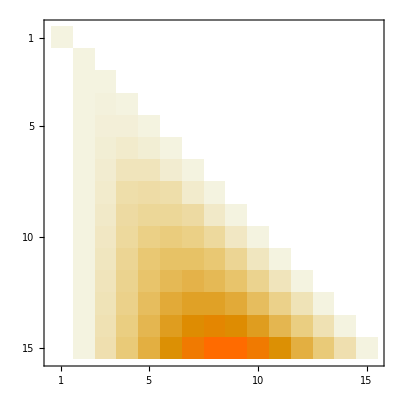

```mathematica
MatrixPlot[thj]
```

```mathematica
Inverse[thj]
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,-2,1,0,0,0,0,0,0,0,0,0,0,0},{0,-1,3,-3,1,0,0,0,0,0,0,0,0,0,0},{0,1,-4,6,-4,1,0,0,0,0,0,0,0,0,0},{0,-1,5,-10,10,-5,1,0,0,0,0,0,0,0,0},{0,1,-6,15,-20,15,-6,1,0,0,0,0,0,0,0},{0,-1,7,-21,35,-35,21,-7,1,0,0,0,0,0,0},{0,1,-8,28,-56,70,-56,28,-8,1,0,0,0,0,0},{0,-1,9,-36,84,-126,126,-84,36,-9,1,0,0,0,0},{0,1,-10,45,-120,210,-252,210,-120,45,-10,1,0,0,0},{0,-1,11,-55,165,-330,462,-462,330,-165,55,-11,1,0,0},{0,1,-12,66,-220,495,-792,924,-792,495,-220,66,-12,1,0},{0,-1,13,-78,286,-715,1287,-1716,1716,-1287,715,-286,78,-13,1}}

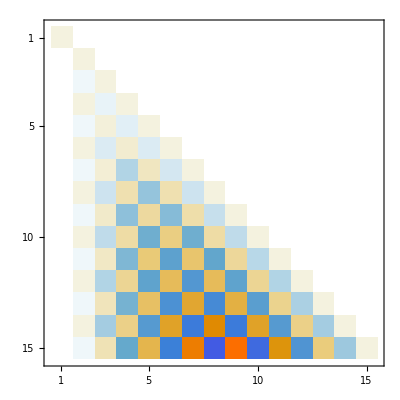

```mathematica
MatrixPlot[Inverse[thj]]
```